```mathematica
Clear["Global`*"]
```

Shortest paths, Moore’s BFS
(All edges length one)
1 - 4 Find a shortest path P:s→t and its length by Moore’s algorithm. Sketch the graph with the labels and indicate P by heavier lines as in figure 482.

7.

```mathematica
outl=Graphics[Line[{{0,0},{1.1,2.2},{3.5,2},{3,0.8},{1.3,0.8},{-1,1.6},{-2.7,0.9},{-3,-1},{-1.5,-2},{0.5,-1.5},{2.7,0}}],ImageSize->250,Axes->True];
```

```mathematica
out2=Graphics[Point[{{0,0},{1.1,2.2},{3.5,2},{3,0.8},{1.3,0.8},{-1,1.6},{-2.7,0.9},{-3,-1},{-1.5,-2},{0.5,-1.5},{2.7,0}}]];
```

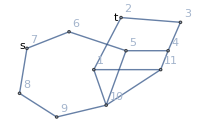

```mathematica
g1=Graph[{1<->2,2<->3,3<->4,4<->5,5<->6,6<->7,7<->8,8<->9,9<->10,10<->11,11<->1,5<->10,4<->11,1<->10},VertexLabels->"Name",VertexCoordinates->{{0,0},{1.1,2.2},{3.5,2},{3,0.8},{1.3,0.8},{-1,1.6},{-2.7,0.9},{-3,-1},{-1.5,-2},{0.5,-1.5},{2.7,0}},Epilog->{{Text[Style["s",Medium],{-2.9,1.}]},{Text[Style["t",Medium],{0.9,2.2}]}},ImageSize->200]
```

```mathematica
GraphDistance[g1,7,2]
```

5

The answer in the above cell matches the answer in the text.

3.

```mathematica
lis={{3.5,2},{3,0.8},{2.7,0},{0,0},{0.5,-1.5},{-1.5,-2},{-3,-1},{-2.7,0.9},{-1,1.6},{1.1,2.2},{1.3,0.8}};
```

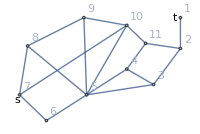

```mathematica
g2=Graph[{1<->2,2<->3,3<->4,4<->5,5<->6,6<->7,7<->8,8<->9,9<->10,10<->11,4<->11,2<->11,3<->5,5<->8,5<->9,5<->10,7<->10},VertexLabels->"Name",VertexCoordinates->{{3,2},{3,0.8},{2,-0.6},{1,0},{-0.5,-1},{-2,-2},{-3,-1},{-2.7,0.9},{-0.6,2},{1,1.7},{1.7,1}},Epilog->{{Text[Style["s",Medium],{-3.1,-1.2}]},{Text[Style["t",Medium],{2.8,2}]}},ImageSize->200]
```

```mathematica
GraphDistance[g2,7,1]
```

4

The answer in the above cell matches the text answer.

5.  Moore’s algorithm. Show that if vertex v has label λ[v] = k, then there is a path s→v of length k.

This is just a matter of organization of the graph.

15 - 17 Euler graphs

15.  An Euler graph G is a graph that has a closed Euler trail. An Euler trail is a trail that contains every edge of G exactly once. Which subgraph with four edges of the graph in example 1, section 23.1, is an Euler graph?

```mathematica
g3=Graph[{1<->2,2<->3,3<->4,4<->1,2<->4},VertexLabels->"Name",VertexCoordinates->{{0,2},{2,2},{0,0},{2,0}},Epilog->{{Text[Style["s",Medium],{-0.15,-0.1}]}},ImageSize->120]
```

-Graphics-

The graph is pictured above. Just from the instructions of the problem, I thought I could see four Eulerian paths: 1-2-4-3-2, 2-3-4-2-1, 3-4-2-1-4, and 4-1-2-4-3, the first two taking out diagonal 1-4, the second taking out diagonal 2-3. These would satisfy the requirement of treading on each edge only once, while visiting all four edges. However, I didn’t notice that the problem specified a closed trail, i.e. the starting vertex must also be the ending one. That requires removal of edge 2-4.

17.  Is the graph shown below an Euler graph?

```mathematica
Graphics[Line[{{0,0},{0.7,1},{2,.4},{4.7,0.4},{6.3,1.1},{7,0}}],ImageSize->400,Axes->True];
```

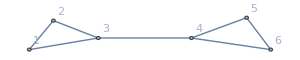

```mathematica
g3=Graph[{1<->2,2<->3,3<->4,4<->5,5<->6,1<->3,4<->6},VertexLabels->"Name",VertexCoordinates->{{0,0},{0.7,1},{2,.4},{4.7,0.4},{6.3,1.1},{7,0}},Epilog->{{Text[Style["s",Medium],{-0.15,-0.1}]}},ImageSize->300]
```

No it is not a Eulerian trail or path, and cannot be one according to the abbreviated description in problem 15, nor according to the Wikipedia description. No way to tread on all edges without repeating edge 3-4.